# Density data plotting code

## Version: 1.3.1

Common

## Directory setting

```mathematica
currentDir=NotebookDirectory[];
SetDirectory[currentDir];
expdir="../../data/density/";
simdir="../simulation/";
matdir="../../DFT code copy/DFFT-master/";
Needs["ErrorBarPlots`"]
```

## File import

### Experiment data

```mathematica
filename="a2021-07-28-02/data";
importdir=expdir;
hdf5File=Import[ToString@Row@{importdir,filename,".hdf5"},"Data"];
```

Import::nffil: File not found during Import.

```mathematica
imstack=hdf5File⟦1,9000;;18000⟧;
Histogram@imstack⟦;;,1,1⟧
```

Part::partd: Part specification $Failed⟦1,9000;;18000⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,9000;;18000⟧⟦1;;All,1,1⟧ is longer than depth of object.

Histogram::ldata: $Failed⟦1,9000;;18000⟧⟦1;;All,1,1⟧ is not a valid dataset or list of datasets.

Histogram[$Failed⟦1,9000;;18000⟧⟦1;;All,1,1⟧]

```mathematica
imstack +=hdf5File⟦1,1;;18000⟧;
Histogram@imstack⟦;;,3,1⟧
```

Part::partd: Part specification $Failed⟦1,1;;18000⟧ is longer than depth of object.

Histogram::ldata: 9001 is not a valid dataset or list of datasets.

Histogram[9001]

### Simulation data

```mathematica
filename="meh";
importdir=simdir;
hdf5File=Import[ToString@Row@{importdir,filename,".hdf5"},"Data"];
```

Import::nffil: File not found during Import.

```mathematica
simstack=hdf5File⟦1,40000;;79999;;150,1,;;,;;⟧;
imstack=simstack;
Histogram@imstack⟦;;,3,1⟧
```

Part::partd: Part specification $Failed⟦1,40000;;79999;;150,1,1;;All,1;;All⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,40000;;79999;;150,1,1;;All,1;;All⟧⟦1;;All,3,1⟧ is longer than depth of object.

Histogram::ldata: $Failed⟦1,40000;;79999;;150,1,1;;All,1;;All⟧⟦1;;All,3,1⟧ is not a valid dataset or list of datasets.

Histogram[$Failed⟦1,40000;;79999;;150,1,1;;All,1;;All⟧⟦1;;All,3,1⟧]

### Matlab data

```mathematica
"Trial_Data/occ_exp";
```

```mathematica
filename="osfstorage-archive/Figure 2/occ_rectangle_96flies";
importdir=matdir;
matFile=Import[ToString@Row@{importdir,filename,".mat"},"Data"]⟦1⟧;
```

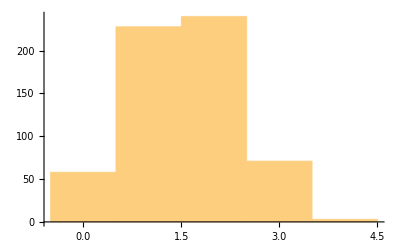

```mathematica
dim1=24;"Sqrt@Length@matFile⟦1⟧";
dim2=2;
imstack=Partition[#,dim1]&/@matFile;
Histogram@imstack⟦;;,-1,1⟧
```

```mathematica
Total@Total@imstack⟦9⟧
```

64.

```mathematica
Max[Total@Total@#&/@imstack]
```

66.

## Parameters

```mathematica
antcount=66;
normfactor=1;
```

Simple average method

## Time integration

### Plot

```mathematica
(*imstack=imstack-Min[imstack];*)
squish=imstack⟦1⟧;
Do[
squish+=imstack⟦i⟧;
,{i,2,Length[imstack]}]
squish/=Length[imstack];
totalantness=antcount Length[imstack];
```

```mathematica
squished=(antcount squish)/(Total@Total@squish);
```

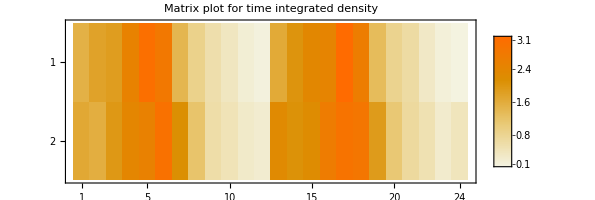

```mathematica
a=Show[MatrixPlot[squished,PlotLegends->Automatic,PlotLabel->"Matrix plot for time integrated density"]]
```

### Figure export

```mathematica
Export[ToString@Row@{filename,"out.png"},a];
```

Export::nodir: Directory C:\Users\MaeLSTRoM\Desktop\Coding\ant\codebase\mathematica\osfstorage-archive\Figure 2\ does not exist.

Export::noopen: Cannot open osfstorage-archive/Figure 2/occ_rectangle_96fliesout.png.

```mathematica
(*antcount/Total[imstack⟦i⟧,{1,2}]*)
```

```mathematica
Directory[]
```

C:\Users\MaeLSTRoM\Desktop\Coding\ant\codebase\mathematica

## Vexation

```mathematica
stackedimstack=imstack;
```

```mathematica
norm=ConstantArray[0,{dim2,dim1}];
```

```mathematica
Do[Do[
norm⟦j,k⟧=Sum[imstack⟦i,j,k⟧/antcount,{i,1,Length[imstack]}]
,{j,1,dim2}],{k,1,dim1}]
```

```mathematica
norm
```

{{12.9697,15.2727,16.2879,21.1364,26.4545,24.303,11.9697,4.57576,1.9697,0.893939,0.424242,0.151515,14.1212,17.4697,20.,20.7273,27.9394,22.3939,10.7273,4.5,2.31818,0.530303,0.242424,0.106061},{14.1364,13.3333,16.7576,20.303,21.2121,26.0758,17.8788,8.69697,2.12121,1.21212,0.515152,0.484848,19.0909,17.6061,18.6364,22.6818,25.5,24.4848,16.3788,7.95455,2.63636,1.54545,0.5,0.969697}}

```mathematica
vexation=-Log[squished norm ];
```

```mathematica
prob=ConstantArray[0,{dim2,dim1}];
n=1;
```

```mathematica
Do[
Do[
prob⟦i,j⟧=Exp[-n vexation⟦i,j⟧]/(norm⟦i,j⟧ Factorial[n]);
,{i,1,dim2}],
{j,1,dim1}]
```

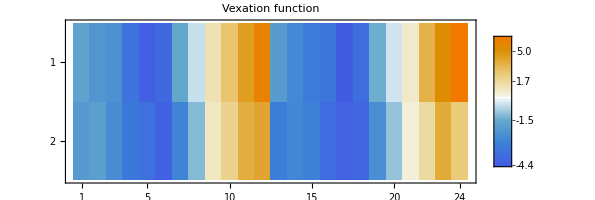

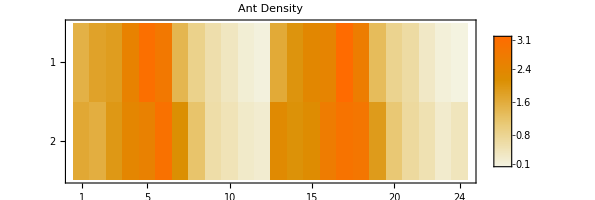

```mathematica
MatrixPlot[vexation,PlotLegends->Automatic,PlotLabel->"Vexation function"]
MatrixPlot[prob,PlotLegends->Automatic,PlotLabel->"Ant Density"]
```

## Symmetrify

```mathematica
halfa=vexation⟦1;;4⟧;
```

Part::take: Cannot take positions 1 through 4 in {{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,0.8145,«6»,-3.89264,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},«1»}.

```mathematica
halfb=vexation⟦5;;8⟧;
```

Part::take: Cannot take positions 5 through 8 in {{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,0.8145,«6»,-3.89264,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},«1»}.

```mathematica
MatrixPlot@Reverse[halfa]
```

Part::pkspec1: The expression {{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,0.8145,«6»,-3.89264,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},«1»} cannot be used as a part specification.

MatrixPlot::mat0: Argument (1;;4)⟦{{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,0.8145,«7»,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},{«1»}}⟧ at position 1 is not a matrix.

MatrixPlot[(1;;4)⟦{{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,0.8145,2.39449,3.88516,5.9444,-3.1251,-3.55068,-3.8212,-3.89264,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},{-3.12724,-3.01027,-3.46744,-3.85128,-3.93889,-4.35175,-3.59697,-2.15569,0.666284,1.78552,3.49685,3.6181,-3.72816,-3.56623,-3.67997,-4.07287,-4.3071,-4.22585,-3.42171,-1.97723,0.231459,1.29962,3.55655,2.2318}}⟧]

```mathematica
halfsum=halfa+Reverse[halfb];
```

Part::pkspec1: The expression {{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,0.8145,«6»,-3.89264,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},«1»} cannot be used as a part specification.

Part::take: Cannot take positions 1 through 4 in {{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,0.8145,«6»,-3.89264,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},«1»}.

Part::pkspec1: The expression {{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,0.8145,«6»,-3.89264,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},«1»} cannot be used as a part specification.

```mathematica
quartera=halfsum⟦;;,1;;4⟧;
quarterb=halfsum⟦;;,5;;8⟧;
```

Part::take: Cannot take positions 1 through 4 in {{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,«8»,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},{-3.12724,«22»,«19»}}⟦1;;4⟧.

Part::take: Cannot take positions 5 through 8 in {{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,«8»,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},{-3.12724,«22»,«19»}}⟦1;;4⟧.

```mathematica
quartersum=quartera+Reverse[quarterb,2];
```

Part::take: Cannot take positions 8 through 5 in {{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,«8»,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},{-3.12724,«22»,«19»}}⟦1;;4⟧.

```mathematica
unfold=ConstantArray[0,{8,8}];
```

```mathematica
Do[Do[
a=Mod[Abs[(-9Quotient[i,5])+Mod[i,5]],5];
b=Mod[Abs[(-9Quotient[j,5])+Mod[j,5]],5];
unfold⟦i,j⟧=quartersum⟦a,b⟧/4.
,{i,1,8}],
{j,1,8}]
```

Part::partw: Part 3 of ({{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,0.8145,«7»,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},{«1»}}⟦1;;4⟧+«1»)⟦«1»⟧«1»«1» does not exist.

Part::partw: Part 4 of ({{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,0.8145,«7»,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},{«1»}}⟦1;;4⟧+«1»)⟦«1»⟧«1»«1» does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
halfa1=norm⟦1;;4⟧;
```

Part::take: Cannot take positions 1 through 4 in {{12.9697,15.2727,16.2879,21.1364,26.4545,24.303,11.9697,4.57576,1.9697,«6»,20.7273,27.9394,22.3939,10.7273,4.5,2.31818,0.530303,0.242424,0.106061},{«1»}}.

```mathematica
halfb1=norm⟦5;;8⟧;
```

Part::take: Cannot take positions 5 through 8 in {{12.9697,15.2727,16.2879,21.1364,26.4545,24.303,11.9697,4.57576,1.9697,«6»,20.7273,27.9394,22.3939,10.7273,4.5,2.31818,0.530303,0.242424,0.106061},{«1»}}.

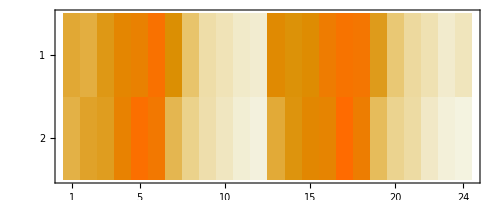

```mathematica
MatrixPlot@Reverse[norm]
```

```mathematica
halfsum1=halfa1+Reverse[halfb1];
```

Part::pkspec1: The expression {{12.9697,15.2727,16.2879,21.1364,26.4545,24.303,11.9697,4.57576,1.9697,«6»,20.7273,27.9394,22.3939,10.7273,4.5,2.31818,0.530303,0.242424,0.106061},{«1»}} cannot be used as a part specification.

```mathematica
quartera1=halfsum1⟦;;,1;;4⟧;
quarterb1=halfsum1⟦;;,5;;8⟧;
```

Part::take: Cannot take positions 1 through 4 in {{12.9697,15.2727,16.2879,21.1364,26.4545,24.303,11.9697,4.57576,1.9697,«6»,20.7273,27.9394,22.3939,10.7273,4.5,2.31818,0.530303,0.242424,0.106061},{«1»}}⟦1;;4⟧.

Part::take: Cannot take positions 5 through 8 in {{12.9697,15.2727,16.2879,21.1364,26.4545,24.303,11.9697,4.57576,1.9697,«6»,20.7273,27.9394,22.3939,10.7273,4.5,2.31818,0.530303,0.242424,0.106061},{«1»}}⟦1;;4⟧.

```mathematica
quartersum1=quartera1+Reverse[quarterb1,2];
```

Part::take: Cannot take positions 8 through 5 in {{12.9697,15.2727,16.2879,21.1364,26.4545,24.303,11.9697,4.57576,1.9697,«6»,20.7273,27.9394,22.3939,10.7273,4.5,2.31818,0.530303,0.242424,0.106061},{«1»}}⟦1;;4⟧.

```mathematica
unfoldnorm=ConstantArray[0,{8,8}];
```

```mathematica
Do[Do[
a=Mod[Abs[(-9Quotient[i,5])+Mod[i,5]],5];
b=Mod[Abs[(-9Quotient[j,5])+Mod[j,5]],5];
unfoldnorm⟦i,j⟧=quartersum1⟦a,b⟧/4.
,{i,1,8}],
{j,1,8}]
```

Part::partw: Part 3 of («1»)⟦1;;All,1;;4⟧+«1» does not exist.

Part::partw: Part 4 of («1»)⟦1;;All,1;;4⟧+«1» does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

FindDivisions::fdargs: The arguments in FindDivisions[{∞,-∞}, 6, 10] are not supported.

FindDivisions::argt: FindDivisions called with 0 arguments; 2 or 3 arguments are expected.

FindDivisions::argtu: FindDivisions called with 1 argument; 2 or 3 arguments are expected.

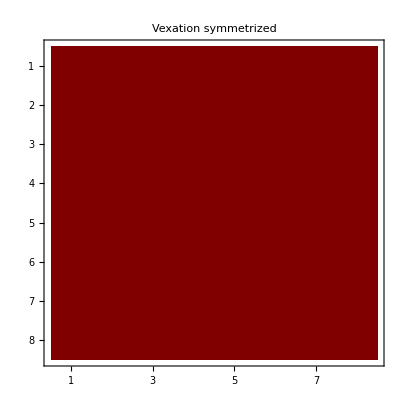

```mathematica
MatrixPlot[unfold,PlotLegends->Automatic,PlotLabel->"Vexation symmetrized"]
```

```mathematica
prob=ConstantArray[0,{8,8}];
n=1;
```

```mathematica
Do[
Do[
prob⟦i,j⟧=Exp[-n unfold⟦i,j⟧]/(unfoldnorm⟦i,j⟧ Factorial[n]);
,{i,1,8}],
{j,1,8}]
```

FindDivisions::fdargs: The arguments in FindDivisions[{∞,-∞}, 6, 10] are not supported.

FindDivisions::argt: FindDivisions called with 0 arguments; 2 or 3 arguments are expected.

FindDivisions::argtu: FindDivisions called with 1 argument; 2 or 3 arguments are expected.

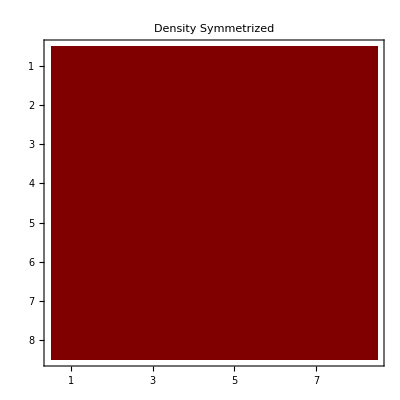

```mathematica
MatrixPlot[prob,PlotLegends->Automatic,PlotLabel->"Density Symmetrized"]
```

## Frustration

```mathematica
(*Needs large number of ants*)
```

```mathematica
(*probf=HistogramList[timesquish,{0.001},"PDF"];*)
probf=HistogramList[normfactor Flatten@imstack,{0,13,1},"PDF"];
probf⟦1⟧=Drop[probf⟦1⟧,-1];
```

```mathematica
frustration[n_,pn_]:=-vexation n - Log[norm Factorial[n] pn];
```

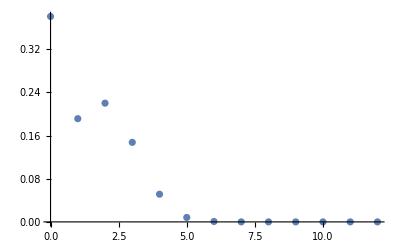

```mathematica
ListPlot@(probfᵀ)
```

```mathematica
frustrray=ConstantArray[0,Length[probf⟦1⟧]];
Do[
frustrray⟦n⟧={probf⟦1,n⟧,Mean@Flatten@frustration[probf⟦1,n⟧,probf⟦2,n⟧]};
,{n,1,Length[frustrray]}]
```

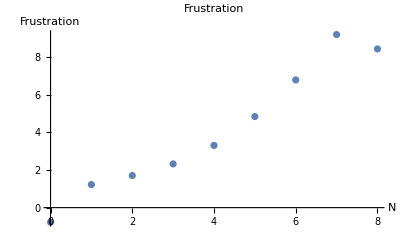

```mathematica
ListPlot[frustrray,PlotLabel->"Frustration", AxesLabel->{"N","Frustration"}]
```

```mathematica
Module[
(* Set local parameters for plotting *)
{data=normfactor Flatten@imstack,
samplesize=0,
flatten=True,
axesLabel={"Number of ants","PDF"},
angularticks=True,
range, ticks, err, dist, hist, len, errors,
bincounts, binwidth, copy, temp},
bincounts=Ceiling@Max@data;
(* Modify structure of data and set up plotting parameters *)
Do[
samplesize+=Length[data⟦i⟧]
,{i,1,Length[data]}];
If[samplesize==0,
samplesize=Length[data]];
If[flatten,data=Flatten[data]];
range={Min[data],Max[data]};
If[angularticks,
ticks={Range[0,Max[data],1],Automatic},
ticks=Automatic];
err={};
Do[
AppendTo[err,ErrorBar[1./(range⟦2⟧-range⟦1⟧),1/Sqrt[samplesize]]];
,{n,1,10}];

(* Generate basic plots using the configs *)
dist=SmoothKernelDistribution[data];
(* Generate histogrambins for further analysis *)
temp={};
hist=HistogramList[data,{Max[data]/bincounts},"PDF"];
len=Length[hist⟦1⟧];
errors={};
Do[
AppendTo[temp,(hist⟦1,i⟧+hist⟦1,i+1⟧)/2.];
binwidth=Max[data]/bincounts;
AppendTo[errors,ErrorBar[binwidth/2.,Sqrt[hist⟦2,i⟧(1-hist⟦2,i⟧binwidth)/(Length[data]binwidth)]]]
,{i,1,Length[hist⟦2⟧]}];
hist={temp,hist⟦2⟧};
copy=histᵀ;
coopy=hist;
hist=Partition[Riffle[histᵀ,errors],2];
(* Generate Error analysis and symmetry analysis plots *)
antcountErrorPlot=ErrorListPlot[hist,PlotRange->{{0,1.05(Max[data]+1)},Full},AxesLabel->axesLabel,PlotLabel->"Histogram of Ant count (With error bars)",PlotStyle->PointSize[0],Joined->True];
];
```

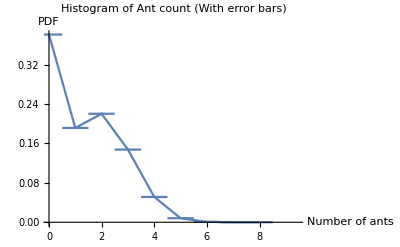

```mathematica
antcountErrorPlot
```

```mathematica
m=1;
frustprob=1/(m!)1/norm(Exp[-vexation]^m Exp[-frustrray⟦m,2⟧]);
```

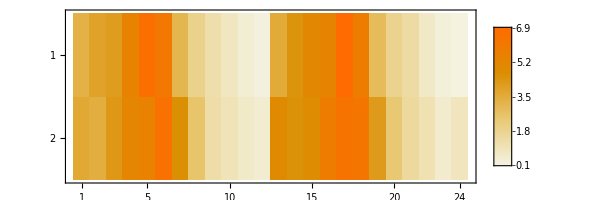

```mathematica
MatrixPlot[frustprob,PlotLegends->Automatic]
```

## Hypothesis testing

### pseudo-free energy

```mathematica
pfe[b1_,b2_,n_]:=-Log[n!HistogramList[normfactor imstack⟦;;,b1,b2⟧,{-0.5,12.5,1},"PDF"]⟦2,n+1⟧];
```

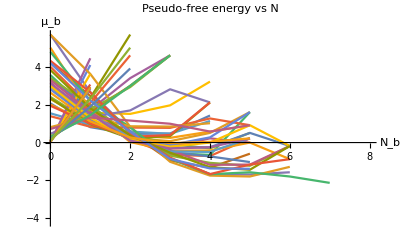

```mathematica
ListPlot[Flatten[Table[{Range[0,12,1],pfe[i,j,Range[0,12,1]]}ᵀ,{i,1,dim2},{j,1,dim1}],1],PlotRange->Full,Joined->True,PlotLabel->"Pseudo-free energy vs N",AxesLabel->{"N_b","μ_b"}]
```

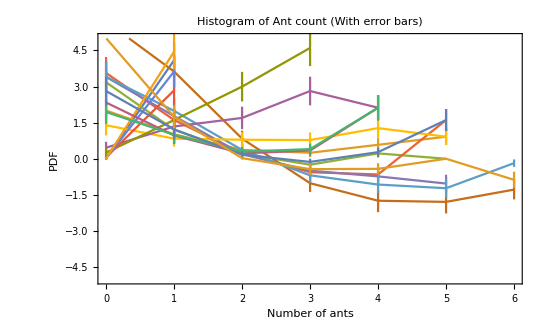

```mathematica
Module[
(* Set local parameters for plotting *)
{datastack=Flatten[Table[{Range[0,12,1],pfe[i,j,Range[0,12,1]]},{i,1,dim2},{j,1,dim1}],1],
samplesize=500,
axesLabel={"Number of ants","PDF"},
angularticks=True,
data,range,ticks,dist,len,errors,
bincounts, binwidth,plottable={}},
bincounts=Ceiling@Max@data;
Do[
data=datastack⟦n,2⟧;
(* Generate Horizontal error bars *)
range=datastack⟦n,1⟧;
(* Generate vertical error bars*)
errors={};
Do[
binwidth=range⟦2⟧-range⟦1⟧;
nnnn=binwidth;
AppendTo[errors,ErrorBar[0,Sqrt[Abs@data⟦i⟧(antcount-Abs@data⟦i⟧binwidth)/(samplesize binwidth)]]]
,{i,1,Length@data}];
AppendTo[plottable,{{range,data}ᵀ,errors}ᵀ],
{n,1,Length[datastack]}];
copy=plottable;
(* Generate Error analysis and symmetry analysis plots *)
pfeErrorPlot=ErrorListPlot[plottable⟦12;;28⟧,PlotRange->{{0,6},{-5,5}},AxesLabel->axesLabel,Frame->True,PlotLabel->"Histogram of Ant count (With error bars)",PlotStyle->PointSize[0],Joined->True]
(*mirror=[-copyᵀ⟦1⟧,Reverse[copyᵀ⟦2⟧];*)(*pfefrustrationErrorPlot=ListPlot[{{ -copyᵀ⟦1⟧,copyᵀ⟦2⟧}ᵀ,copy},PlotRange->{{0,Automatic},Full},PlotLabel->"Left-Right comparison for angular velocity distribution",PlotLegends->{"Left","Right"},ImageSize->700,Ticks->ticks,AxesLabel->{"Angular velocity (rad/s)", "PDF"},Joined->True];*)
];
pfeErrorPlot
```

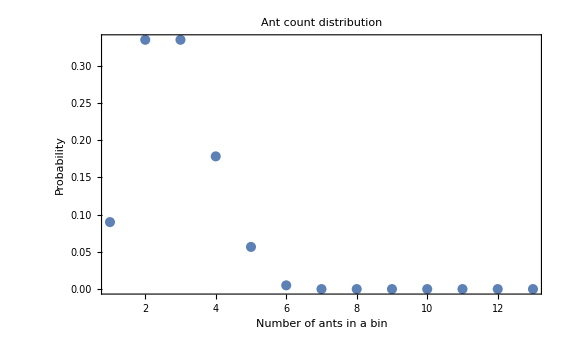

```mathematica
check=HistogramList[normfactor imstack⟦;;,1,3⟧,{-0.5,12.5,1},"PDF"]⟦2⟧;
ListPlot[check,PlotRange->Full,PlotLabel->"Ant count distribution",Frame-> True, FrameLabel->{"Number of ants in a bin", "Probability"}]
```

```mathematica
(* Subscript[f, b] = -ln(N!P(N)) - Subscript[v, b] N - ln(Subscript[z, b]) *)
```

```mathematica
fN[i_,j_,n_]:=pfe[i,j,n]-( vexation⟦i,j⟧n+Log[ norm⟦i,j⟧]);
```

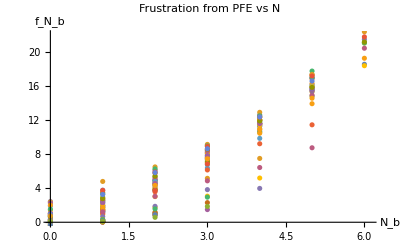

$Aborted[]

Part::partw: Part {1,2,3,4,5,6,7,8,9,10,11,12,13} of {-0.5,12.5,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ListPlot[Flatten[Table[{Range[0,12,1],fN[i,j,Range[0,12,1]]}ᵀ,{i,1,dim2},{j,1,dim1}],1],Joined->False,PlotLabel->"Frustration from PFE vs N",AxesLabel->{"N_b","f_N_b"},PlotRange->{{0,6.1},{0,22}}]
```

```mathematica
filename="Trial_Data/vmle";
importdir=matdir;
vexcheck=Import[ToString@Row@{importdir,filename,".mat"},"Data"];
```

```mathematica
vexcheck=Partition[Flatten@vexcheck,24];
```

```mathematica
GraphicsColumn[{MatrixPlot[vexcheck,ImageSize->300,PlotLegends->Automatic,FrameTicks-> False],MatrixPlot[vexation,ImageSize->300,PlotLegends->Automatic,FrameTicks-> False]}]
```

```mathematica
Total@Total@vexcheck
```

1.52845

```mathematica
Total@Total@vexation
```

-63.1407

```mathematica
Log@norm
```

{{2.56262,2.72607,2.79042,3.05099,3.27543,3.1906,2.48238,1.52077,0.67788,-0.112117,-0.85745,-1.88707,2.64768,2.86047,2.99573,3.03145,3.33004,3.10879,2.37279,1.50408,0.840783,-0.634307,-1.41707,-2.24374},{2.64875,2.59027,2.81885,3.01077,3.05457,3.26101,2.88361,2.16297,0.751988,0.192372,-0.663294,-0.723919,2.94921,2.86824,2.92511,3.12156,3.23868,3.19805,2.79599,2.07374,0.969401,0.435318,-0.693147,-0.0307717}}

```mathematica
vexation
```

{{-2.95497,-3.28188,-3.41058,-3.93173,-4.3806,-4.21094,-2.7945,-0.871285,0.8145,2.39449,3.88516,5.9444,-3.1251,-3.55068,-3.8212,-3.89264,-4.48982,-4.04732,-2.57532,-0.837895,0.488693,3.43887,5.00439,6.65775},{-3.12724,-3.01027,-3.46744,-3.85128,-3.93889,-4.35175,-3.59697,-2.15569,0.666284,1.78552,3.49685,3.6181,-3.72816,-3.56623,-3.67997,-4.07287,-4.3071,-4.22585,-3.42171,-1.97723,0.231459,1.29962,3.55655,2.2318}}

```mathematica
vexcheck
```

{{-0.738161,-1.00869,-1.12373,-1.65319,-2.21166,-1.98813,-0.614948,0.596426,1.49748,2.3063,3.05883,4.09231,-0.875361,-1.25537,-1.53125,-1.60941,-2.36353,-1.78702,-0.454987,0.615044,1.32779,2.83413,3.62102,4.44959},{-0.877138,-0.781972,-1.17631,-1.56387,-1.66129,-2.17257,-1.30047,-0.170095,1.42048,1.9966,2.86335,2.92442,-1.43291,-1.27043,-1.38344,-1.8175,-2.11292,-2.00715,-1.13394,-0.0556674,1.19269,1.74786,2.89343,2.2238}}

Maximum Likelihood Estimation method (MLE)

```mathematica
(*
Outline.
Find the minimum of g(Vex,Frus)=-log(P(V,f|Data)), using preconditioned conjugate gradient. The arguments of g(V,F) at the minimum gives us the maximum likelihood estimates for the parameters used for the model. The values F(0) and F(1) are constrained at 0 so that the covariance matrix is non-singular, and there is asymptotic limit for distribution of estimators.
Source:
Pseudocode published by 
*)
```